# Chapter 5-CIRCULAR MOTION—GRAVITATION

Peter Burbery

Abstract

## Section

XXXX:

## 5-1 to 5-3 Uniform Circular Motion

### 1. (I) A child sitting 1.20 m from the center of a merry-go-round moves with a speed of 1.10 m·s^-1. Calculate {a} the centripetal acceleration of the child and {b} the net horizontal force exerted on the child (mass=22.5 kg).

View possible formulas for centripetal acceleration:

```mathematica
AssociationMap[FormulaData][FormulaLookup["CentripetalAcceleration"]]
```

<|{CentripetalAcceleration,RotationSpeed}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,AngularVelocity}→a Acceleration==r Radius (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,Diameter}→a Acceleration==1/2 d Diameter (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{CentripetalAcceleration,OrbitSpeed}→a Acceleration==(v Speed)^2/(d_o Distance),{CentripetalAcceleration,OrbitSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,OrbitSpeed,Radius}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,RotationRate}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius,{CentripetalAcceleration,RotationRate,Diameter}→a Acceleration==(2 π^2 /rev^2) d Diameter (n RevolutionRate)^2,{CentripetalAcceleration,RotationRate,OrbitDistance}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 d_o Distance,{CentripetalAcceleration,RotationSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,RotationSpeed,OrbitDistance}→a Acceleration==(v Speed)^2/(d_o Distance)|>

I will use the formula CentripetalAcceleration with RotationSpeed.

Get data for the formula:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"}]
```

a Acceleration==(v Speed)^2/(r Radius)

The table has lots of helpful information:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | centripetal acceleration | Acceleration | {{LengthUnit,1},{TimeUnit,-2}}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

#### Formula Classes

I wonder what classes this formula is in.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"Classes"]
```

{Physics,{Physics,Mechanics}}

I wonder what other formulas are in the classes:

Make a word cloud for each class:

```mathematica
PersistResourceFunction["FromCamelCase"]
```

Success[…]

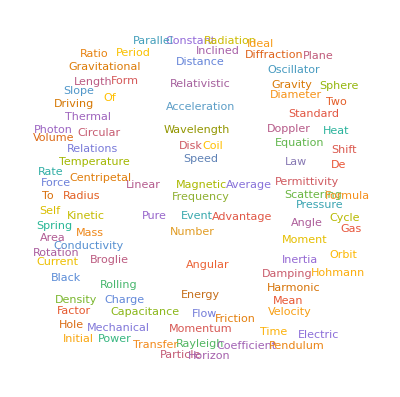

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup["Physics"]]]]
```

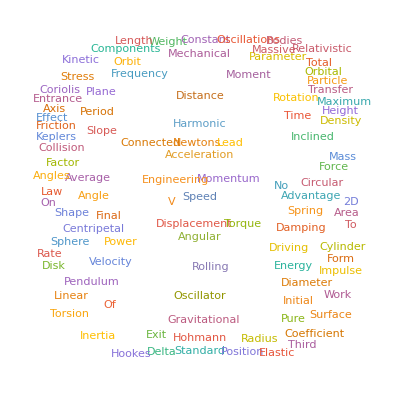

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup[{"Physics","Mechanics"}]]]]
```

#### using the formula for part a

The child is sitting 1.20m from the merry-go-round so the radius is 1.20m. The speed or velocity is 1.10 m·s^-1.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]
```

{a Acceleration,r Radius,v Speed}

I just need the rest of the variables, not a:

```mathematica
Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]
```

{r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]->{Quantity[1.2, "Meters"],Quantity[1.1, ("Meters")/("Seconds")]}]
```

<|r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules
```

a Acceleration==1.00833 m/s^2

I'm curious what a rationalized form of this is.

```mathematica
Rationalize[FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules]
```

a Acceleration==121/120 m/s^2

#### part b

```mathematica
substitutionRules//=AppendTo[First[]]
```

```mathematica
FormulaLookup["CentripetalForce"]
```

{{CentripetalForce,RotationSpeed},{CentripetalForce,AngularVelocity}}

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]
```

{m Mass,r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]->Prepend[(Quantity[22.5, "Kilograms"])][Values[substitutionRules]]]
```

<|m Mass→22.5 kg,r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules
```

F Force==22.6875 kg m/s^2

```mathematica
Rationalize[FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules]
```

F Force==363/16 kg m/s^2

#### Notes

I reworded the question.

The original question was

A child sitting 1.20 m from the center of a merry-go-round moves with a speed of 1.10 m/s. Calculate (a) the centripetal acceleration of the child and (b) the net horizontal force exerted on the child (mass=22.5 kg).

I think scientific notation is universally better to use than the oblique stroke / for division. For example  1.10 m·s^-1, written in scientific notation, and 1.10 m/s, written with the oblique stroke for division, are equivalent. However, I would like to mention that scientific notation requires less parentheses and often leads to less confusion. Scientific notation is a powerful way to cover complicated cases whereas division is not. For example, here are several things scientific notation can do that you can't do very well with the / marker or not at all.

The zeroeth exponent. m^0. This has the value 1 except for when you have 0^0. I guess you could write m/m, but I think m^0 is easier to understand.

The plus one exponent. For example m^1 has the value 1.

```mathematica
0^0
```

Indeterminate

```mathematica
100^(2^-1)
```

10

```mathematica
100^(2^-1)
```

10

```mathematica
a^(b^-c)
```

a^(b^-c)

```mathematica
a^(b^-c)===a^(b^-c)
```

True

```mathematica
a^(b^(-c^-d))==a^(b^(-c^-d))
```

True

I wrote down some more of my thoughts on the benefits of this. The files were too large but I made them available in a Google Photos link.

I wrote down some more of my thoughts on the benefits of this at https://photos.app.goo.gl/yWMGanjf6bZ7AMh58 and https://photos.app.goo.gl/dPKd678dtDfkTd3n6.

This is from the quaternion page on wikipedia:

### 3. (I) A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm's length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

#### Initial work

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
F | centripetal force | Force | {{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}
m | mass | Mass | {MassUnit,1}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed"]
```

{{v Speed→-(√(F Force) √(r Radius))/(√(m Mass))},{v Speed→(√(F Force) √(r Radius))/(√(m Mass))}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",]
```

{{v Speed→ConditionalExpression[√((F Force r Radius)/(m Mass)), F Force>0&&m Mass>0&&r Radius>0]}}

```mathematica
#>0&/@FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]
```

{F Force>0,m Mass>0,r Radius>0,v Speed>0}

```mathematica
Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]
```

F Force>0&&m Mass>0&&r Radius>0

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]
```

{{v Speed→√((F Force r Radius)/(m Mass))}}

```mathematica
substitutionRules=AssociationThread[{"F" "Force","r" "Radius","m" "Mass"}->{Quantity[310, "Newtons"],Quantity[900, "Millimeters"],Quantity[2., "Kilograms"]}]
```

<|F Force→310 N,r Radius→900 mm,m Mass→2. kg|>

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules
```

{{v Speed→373.497 √mm √N/√kg}}

```mathematica
UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]
```

{{v Speed→11.811 m/s}}

```mathematica
Rationalize[UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]]
```

{{v Speed→11.811 m/s}}

#### Notes and comments

I reworded this problem slightly to use millimeters in place of millimeters to be in accordance with NIST SP 811 Chapter 7 Section 9 Choosing SI Prefixes. The original wording was

A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm’s length) uniformly in a horizontal circle of radius 0.90 m. Calculate the speed of the ball.

There is a discrepancy here in that when I say 900 mm I have three significant figures but 0.90 m has only two significant figures. I changed this to 900 mm even though there was a discrepancy because it realistic to measure something to nearest millimeter instead of to the nearest centimeter, which is the practice in metric architecture and CAD where all dimensions are in millimeters. If this discrepancy is to be avoided, the problem should solved with something like 9.0E2 mm. If 3 significant figures were known, as is the case for 900 mm, I would write 9.00E2 mm.

There is one other thing with this that I think should be changed which instead of saying a 2.0-kg ball, something like a ball of mass 2.0 kg is better. This is explained in NIST SP 811 Chapter 7 Section 2 Space between numerical value and unit symbol.

In summary, I would revise the question to something like this:

A horizontal force of 310 N is exerted on a ball of mass 2.0 kg as it rotates (at arm’s length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

### 5. (II) A 0.55-kg ball, attached to the end of a horizontal cord, is revolved in a circle of radius 1.3 m on a frictionless horizontal surface. If the cord will break when the tension in it exceeds 75 N, what is the maximum speed the ball can have?

I will reword this to:

A ball of mass 550g, attached to the end of a horizontal cord, is revolved in a circle of radius 1.3 m on a frictionless horizontal surface. If the cord will break when the tension in it exceeds 75 N, what is the maximum speed the ball can have?

```mathematica
substitutionRules=AssociationThread[{"m" "Mass","r" "Radius","F" "Force"}->{Quantity[550, "Grams"],Quantity[1.3, "Meters"],Quantity[75, "Newtons"]}]
```

<|m Mass→550 g,r Radius→1.3 m,F Force→75 N|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules
```

75 N==(423.077 g/m) (v Speed)^2

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",]
```

{{v Speed→13.3144 m/s}}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]
```

{v Velocity==4608866/346157 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]]
```

{v Velocity==13.3144 m/s}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]
```

{v Velocity==436898813/32814055 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]]
```

{v Velocity==13.3144 m/s}

### 49. (II) Calculate the period of a satellite orbiting the Moon 95 km above the Moon's surface. Ignore effects of the Earth. The radius of the Moon is 1740 km.

I will reword this to:

I) Calculate the period of a satellite orbiting the Moon 95 km above the Moon’s surface. Ignore effects of the Earth. The radius of the Moon is 1.740 Mm.

```mathematica
FormulaLookup["Mechanics"]
```

{HollowCylinderMechanicalStress,LeverMechanicalAdvantage,MechanicalStress,PulleySystemMechanicalAdvantage,WheelAndAxleMechanicalAdvantage,{CylinderMechanicalStress,Diameter},{CylinderMechanicalStress,Radius},{InclinedPlaneMechanicalAdvantage,LengthHeight},{InclinedPlaneMechanicalAdvantage,Slope},{ScrewMechanicalAdvantage,Lead},{ScrewMechanicalAdvantage,LeadAngle},{WedgeMechanicalAdvantage,Angle},{WedgeMechanicalAdvantage,LengthThickness},{MechanicalPower,Force,Speed},{MechanicalPower,Work,Time},{MechanicalPower,Force,Speed,Angle}}

```mathematica
FormulaData["StefanBoltzmannLaw","Classes"]
```

{Physics,{Physics,Thermodynamics}}

```mathematica
FormulaData["LuminosityEnergy","Classes"]
```

{Space,{Space,Astronomy}}

```mathematica
FormulaLookup["Space"]
```

{ApparentMagnitudeIntensity,DistanceModulus,DrakeEquation,{JeansLength,SoundSpeed},{JeansLength,Temperature,MeanMass},{JeansMass,SoundSpeed},{JeansMass,Temperature,MeanMass},LuminosityAbsoluteMagnitude,LuminosityApparentMagnitudeDistance,LuminosityDistance,LuminosityEnergy,MassLuminosityRelationship,ParallaxDistance,SeagerEquation,{BlackHoleEntropy,Standard},{BlackHoleEntropy,Charge},{BlackHoleEntropy,Charge,AngularMomentum},{BlackHoleEntropy,AngularMomentum},BlackHoleHawkingRadiationPower,BlackHoleLifetime,{BlackHoleSurfaceGravity,Standard},{BlackHoleSurfaceGravity,Charge},{BlackHoleSurfaceGravity,Charge,AngularMomentum},{BlackHoleSurfaceGravity,AngularMomentum},{BlackHoleTemperature,Standard},{BlackHoleTemperature,Charge},{BlackHoleTemperature,Charge,AngularMomentum},{BlackHoleTemperature,AngularMomentum},{BlackHoleEventHorizonRadius,Standard},{BlackHoleEventHorizonRadius,Charge,AngularMomentum},{BlackHoleEventHorizonRadius,Charge},{BlackHoleEventHorizonRadius,AngularMomentum},{BlackHoleEventHorizonArea,Standard},{BlackHoleEventHorizonArea,Charge,AngularMomentum},{BlackHoleEventHorizonArea,Charge},{BlackHoleEventHorizonArea,AngularMomentum},{RedshiftWavelength,Wavelength},{RedshiftWavelength,Frequency},{CircularOrbitSpeed,OrbitRadius},{CircularOrbitSpeed,Altitude},EarthCircularOrbitPeriod,EllipticOrbitFormula,EscapeVelocity,HohmannAngularAlignment,{HohmannEntranceDeltaV,Mass},{HohmannEntranceDeltaV,GravitationalParameter},{HohmannExitDeltaV,Mass},{HohmannExitDeltaV,GravitationalParameter},{HohmannTotalDeltaV,Mass},{HohmannTotalDeltaV,GravitationalParameter},{HohmannTransferTime,OrbitalRadii,Mass},{HohmannTransferTime,OrbitalRadii,GravitationalParameter},{HohmannTransferTime,SemimajorAxis,Mass},{HohmannTransferTime,SemimajorAxis,GravitationalParameter},KeplersFirstLaw,{KeplersThirdLaw,Sun},{KeplersThirdLaw,SingleMass},{KeplersThirdLaw,Masses},RocketEquation,{VisViva,Mass},{VisViva,GravitationalParameter},{BussardRamjet,PhotonDrive},{BussardRamjet,MatterDrive},{BlackbodyLuminosity,Radius},{BlackbodyLuminosity,Diameter}}

```mathematica
FormulaData[]
```

```mathematica
Entity["PlanetaryMoon","Moon"]["Mass"]
```

7.346×10^22 kg

```mathematica
Solve[Entity["PhysicalConstant","GravitationalConstant"]("m" "Mass")/("h" "Height"+Entity["PlanetaryMoon","Moon"]["Radius"])^2=="m" "Mass" ("(""h" "Height"+Entity["PlanetaryMoon","Moon"][Radius]) "Speed")^2/("h" "Height"+Entity["PlanetaryMoon","Moon"]["Radius"]),]
```

```mathematica
substitutionRules=AssociationThread[{"m" "Mass","r" "Radius","F" "Force"}->{Quantity[550, "Grams"],Quantity[1.3, "Meters"],Quantity[75, "Newtons"]}]
```

<|m Mass→550 g,r Radius→1.3 m,F Force→75 N|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules
```

75 N==(423.077 g/m) (v Speed)^2

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",]
```

{{v Speed→13.3144 m/s}}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]
```

{v Velocity==4608866/346157 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]]
```

{v Velocity==13.3144 m/s}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]
```

{v Velocity==436898813/32814055 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]]
```

{v Velocity==13.3144 m/s}

The gravitational constant G:

```mathematica
DeleteMissing[Entity["PhysicalConstant","GravitationalConstant"]["PropertyAssociation"]]
```

<|abbreviation code→bg,ASCII description→Newtonian constant of gravitation,classes→{CODATA constants,cosmological constants,gravitational constants,Wolfram legacy package},conjectured value association→{Fuerth1929→{Name→Fürth,DOI→10.1007/BF01340273,ExternalLink→https://link.springer.com/article/10.1007/BF01340273,Source→{Alexander Kritov.   A New Large Number Numerical Coincidences.  PROGRESS IN PHYSICS, Volume 2, 25-28, 2013.,R. Fürth  ''Über einen Zusammenhang zwischen quantenmechanischer Unscäarfe und Struktur der Elementarteilchen und seine hierauf begründete Berechnung der Massen von Proton und Elektron,'' Zeitschrift für Physik 57 (1929), 429--446.},Authors→{ReinholdFuerth},Value→1.7414061×10^-45 ℏ c/m_e^2,Year→1929},Good1970a→{Name→Good,DOI→10.1016/0375-9601(70)90843-1,ExternalLink→http://www.sciencedirect.com/science/article/pii/0375960170908431,Source→{Good, I.J.  The proton and neutron masses and a conjecture for the gravitational constant. Physics Letters 33A, 383-384, 1970.},Authors→{IJGood},Value→742152508482333333658670581797279093878779454435134458830374627054384976137819329710991160696038985158454890752258637548762597143650054931640625/(10328999512347634358623676688012047497318823171316894051322637426162590488067364778518581413120551325743612687890989973504 π^136) ℏ c/m_e^2,Year→1970},Good1970b→{Name→Good,DOI→10.1016/0375-9601(70)90843-1,ExternalLink→http://www.sciencedirect.com/science/article/pii/0375960170908431,Source→{Good, I.J.  The proton and neutron masses and a conjecture for the gravitational constant. Physics Letters 33A, 383-384, 1970.},Authors→{IJGood},Value→9.3271566×10^-50 ℏ c/(α^2 m_e^2),Year→1970},Kritov2013→{Name→Kritov,DOI→Missing[NotAvailable],ExternalLink→http://www.ptep-online.com/2013/PP-33-07.PDF,Source→{Alexander Kritov.   A New Large Number Numerical Coincidences.  PROGRESS IN PHYSICS, Volume 2, 25-28, 2013.},Authors→{AlexanderKritov},Value→3/(27222589353675077077069968594541456916480 π) e^2/(m_e m_p ε_0),Year→2013}},conjectured values→{1.7414061×10^-45 ℏ c/m_e^2,742152508482333333658670581797279093878779454435134458830374627054384976137819329710991160696038985158454890752258637548762597143650054931640625/(10328999512347634358623676688012047497318823171316894051322637426162590488067364778518581413120551325743612687890989973504 π^136) ℏ c/m_e^2,9.3271566×10^-50 ℏ c/(α^2 m_e^2),3/(27222589353675077077069968594541456916480 π) e^2/(m_e m_p ε_0)},description→Newtonian constant of gravitation,entity classes→{CODATA constants,cosmological constants,gravitational constants,Wolfram legacy package},equivalent forms→{(1 /M_♁)×( (GM)_♁),(1 /M_☉)×( (GM)_☉),(1 /m_P^2)×( ℏ)×( c),1/2×1/π×( h)×(1 /m_P^2)×( c),1/8×1/π×(1 m_e^2)×(1 α^4)×(1 /h)×(1 /m_P^2)×(1 /R_∞^2)×(1 c^3),1/16×1/π^2×(1 m_e^2)×(1 α^4)×(1 /m_P^2)×(1 /ℏ)×(1 /R_∞^2)×(1 c^3),1/8×1/π×( κ)×(1 c^4)},Lévy-Leblond class→C,name→gravitational constant,primary source→CODATA2018,quantity→ G,relative uncertainty→0.0000224743,standard uncertainty→1.5×10^-15 m^3/(kg s^2),standard year→Year: 2018,symbol→G,value→6.674×10^-11 m^3/(kg s^2),value association→{AstronomicalAlmanac2018→{Description→constant of gravitation,StandardBody→AstronomicalAlmanac,StandardYear→2018,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},CODATA1969→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1969,Symbol→G,Value→6.6732×10^-11 m^3/(kg s^2),StandardUncertainty→3.1×10^-14 m^3/(kg s^2)},CODATA1973→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1973,Symbol→G,Value→6.672×10^-11 m^3/(kg s^2),StandardUncertainty→4.1×10^-14 m^3/(kg s^2)},CODATA1986→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1986,Symbol→G,Value→6.67259×10^-11 m^3/(kg s^2),StandardUncertainty→8.5×10^-15 m^3/(kg s^2)},CODATA1998→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1998,Symbol→G,Value→6.673×10^-11 m^3/(kg s^2),StandardUncertainty→1.×10^-13 m^3/(kg s^2)},CODATA2002→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2002,Symbol→G,Value→6.6742×10^-11 m^3/(kg s^2),StandardUncertainty→1.×10^-14 m^3/(kg s^2)},CODATA2006→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2006,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},CODATA2010→{ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2010,Symbol→G,Value→6.67384×10^-11 m^3/(kg s^2),StandardUncertainty→8.×10^-15 m^3/(kg s^2)},CODATA2014→{ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2014,Symbol→G,Value→6.67408×10^-11 m^3/(kg s^2),StandardUncertainty→3.1×10^-15 m^3/(kg s^2)},CODATA2018→{AbbreviationCode→bg,ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2018,Symbol→G,Value→6.6743×10^-11 m^3/(kg s^2),StandardUncertainty→1.5×10^-15 m^3/(kg s^2)},IAU2009→{Description→constant of gravitation,StandardBody→IAU,StandardYear→2009,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},LiEtAl2018TOS→{Description→Newtonian gravitational constant,StandardYear→2018,Value→6.67418×10^-11 m^3/(kg s^2),StandardUncertainty→7.8×10^-16 m^3/(kg s^2)},LiEtAl2018AAF→{Description→Newtonian gravitational constant,StandardYear→2018,Value→6.67448×10^-11 m^3/(kg s^2),StandardUncertainty→7.8×10^-16 m^3/(kg s^2)},WolframLegacyPackage→{Description→GravitationalConstant is the coefficient of proportionality in Newton's law of gravitation.,PackageSymbol→GravitationalConstant,Value→6.67428×10^-11 m^2 N/kg^2}},values→{6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.7×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.7×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.67428×10^-11 m^2 N/kg^2},variants→{GravitationalConstantWGS84},variant table→GravitationalConstant | 6.674×10^-11 m^2 N/kg^2
GravitationalConstantWGS84 | 6.673×10^-11 m^2 N/kg^2|>

```mathematica
Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]] "m" "Mass" (Subscript["m", "Moon"] "Mass")/("r" "Radius")^2=="m" "Mass" ("v" "Speed")^2/("r" "Radius")
```

```mathematica
InputForm[((Quantity[6.674299999999999379001243669`4.347284468938097*^-11, ("Meters")^3/("Kilograms" ("Seconds")^2)]) "m" "Mass" Subscript["m", "Moon"] "Mass")/("r" "Radius")^2==("m" "Mass" ("v" "Speed")^2)/("r" "Radius")]
```

(Quantity[6.674299999999999379001243669`4.347284468938097*^-11, "Meters"^3/("Kilograms"*"Seconds"^2)]*QuantityVariable["m", "Mass"]*
   QuantityVariable[Subscript["m", "Moon"], "Mass"])/QuantityVariable["r", "Radius"]^2 == 
 (QuantityVariable["m", "Mass"]*QuantityVariable["v", "Speed"]^2)/QuantityVariable["r", "Radius"]

```mathematica
eqn=Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]] "m" "Mass" (Subscript["m", "Moon"] "Mass")/("r" "Radius")^2=="m" "Mass" ("v" "Speed")^2/("r" "Radius")
```

((6.674×10^-11 m^3/(kg s^2)) m Mass m_Moon Mass)/(r Radius)^2==(m Mass (v Speed)^2)/(r Radius)

```mathematica
radiusRule=AssociationThread[{"r" "Radius"}->{"h" "Height"+Entity["PlanetaryMoon","Moon"][]}]
```

Moon data

```mathematica
DeleteMissing[Entity["PlanetaryMoon","Moon"]["PropertyAssociation"],Infinity,Infinity]
```

<|absolute magnitude H→0.2,age→4.53×10^9 yr,albedo→0.12,alphanumeric name→Moon,alternate names→{Luna},altitude→-30 -40,next maximum altitude→71 25.9238,next transit altitude→72 59.89,angular diameter→30.153 ',angular radius→15.076 ',largest distance from orbit center→406000. km,next apoapsis time→Sun 8 Jan 2023 04:20:00GMT-5,last apoapsis time→Sun 11 Dec 2022 19:30:00GMT-5,apparent altitude→1 55.384,apparent magnitude→-11.4,longitude of ascending node Ω→125.08 °,atmospheric composition→<|helium-4→26.  vol%,neon-20→26.  vol%,hydrogen→23.  vol%,argon-40→19.  vol%,neon-22→3.2  vol%,argon-36→1.3  vol%,methane→0.65  vol%,ammonia→0.65  vol%,carbon dioxide→0.65  vol%|>,atmospheric pressure→3.×10^-15 bar,average distance from Earth→0.00257 au,average orbit distance→0.00257 au,average orbit velocity→1.02 km/s,average temperature→-36. °C,azimuth→17 12,azimuth at rise→64 27.7,azimuth at set→298 33.8,above the horizon→False,classes→{Earth moons,largest moons},color→color red:0.586 green:0.534 blue:0.517,constellation→Aries,cylindrical equidistant texture→-Graphics-,daily time above horizon→10 10.,declination→19 4,mean density→3.344 g/cm^3,average diameter→3474.8 km,dimensions→{3474.8 km,3474.8 km,3474.8 km},distance from Earth→396165. km,distance from Sun→0.985086 au,eccentric anomaly→119 51.4694,orbital eccentricity→0.0554,effective temperature→268. K,entity classes→{Earth moons,largest moons},equatorial angular velocity→13.176358 °,equatorial circumference→10921. km,equatorial diameter→3476.2 km,equatorial diameter along orbit→3474.8 km,equatorial diameter toward planet→3474.8 km,equatorial frequency→2.6616995×10^-6 Hz,equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,escape velocity→2374.93 m/s,farthest planet→Neptune,galactic latitude→-29 -25,galactic longitude→166 0,geocentric ecliptic latitude→17 47.5,geocentric ecliptic longitude→54 4,gravitational constant mass product→4.9028×10^12 m^3/s^2,gravity→1.6232 m/s^2,Greenwich hour angle→277.659 °,heliocentric ecliptic latitude→10.5 ",heliocentric ecliptic longitude→101 50,heliocentric XYZ coordinates→{-0.202139 au,0.964124 au,0.0000501466 au},Hill radius→58100. km,image→-Graphics-,orbital inclination→5.16 °,local hour angle→195.217 °,orbital major axis→768800. km,mass→7.346×10^22 kg,next maximum altitude time→Minute: Mon 2 Jan 2023 21:29GMT-5,maximum temperature→100. °C,minimum temperature→-173. °C,orbital minor axis→768000. km,rotational moment of inertia→8.7×10^34 kg m^2,NAIF identifier→301,name→Moon,nearest planet→Earth,object type→PlanetaryMoon,obliquity→1.5424 °,orbital angular momentum→2.871×10^34 s J,orbital kinetic energy→3.582×10^28 J,orbital moment of inertia→1.09×10^40 kg m^2,orbit center→Earth,orbit circumference→2.4134×10^6 km,orbital period→27.322 days,smallest distance from orbit center→363000. km,argument of periapsis ω→318.15 °,next periapsis time→Sat 21 Jan 2023 15:53:00GMT-5,last periapsis time→Sat 24 Dec 2022 03:32:00GMT-5,polar diameter→3472. km,polar radius→1736. km,average radius→1737.4 km,apparent direction→prograde,right ascension→3 26,next rise→Minute: Mon 2 Jan 2023 14:07GMT-5,Roche limit→18000. km,rotational angular momentum→2.3×10^29 s J,rotation period→27.321661 days,orbital semimajor axis→384400. km,orbital semiminor axis→384000. km,next set→Minute: Tue 3 Jan 2023 05:01GMT-5,shape→sphere,sidereal hour angle→308.381 °,solar day→29.53059 days,solid angle→0.00006042 sr,stationary orbit radius→88450. km,stationary orbit speed→0.2354 km/s,elongation from the Sun→128 25,surface area→3.8×10^7 km^2,3D graphic→-Graphics3D-,next transit time→Minute: Mon 2 Jan 2023 21:29GMT-5,true anomaly→122 34.4887,volume→2.2×10^19 m^3,zenith angle→120 40|>